# Graph Theory

## Enter subtitle here

Enter subsubtitle here

## Enter section title here

### Enter subsection title here

#### Enter subsubsection title here

Enter text here. Enter TraditionalForm input for evaluation in a separate cell below:

```mathematica
∫xⅆx+√z
```

x^2/2+√z

Enter bulleted item text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

Enter text here. Enter formula for display in a separate cell below:

∫xⅆx+√z

Enter text here. Enter an inline formula like this: 2+2.

Enter numbered item text here.

Enter item paragraph text here.

Enter numbered subitem text here.

Enter item paragraph text here.

Enter subitem text here.

Enter item paragraph text here.

A graph 𝒢 has a vertex set 𝒱 and an edge set ℰ. The definition of a subgraph.

A graph 𝒢 is a subgraph of graph ℋ if and only if 𝒱(𝒢)⊆𝒱(ℋ) and ℰ(𝒢)⊆ℰ(ℋ). In math notation 𝒢 is a subgraph of ℋ ⇔𝒱(𝒢)⊆ and

∫xⅆx+√z

Enter text here. Enter Wolfram Language program code below.

```mathematica
fun[x_]:=1
```

Enter text here. Enter non-Wolfram Language program code below.

DLLEXPORT int fun(WolframLibraryData libData, mreal A1, mreal *Res)
{
 mreal R0_0;
 mreal R0_1;
 R0_0 = A1;
 R0_1 = R0_0 * R0_0;
 *Res = R0_1;
 funStructCompile->WolframLibraryData_cleanUp(libData, 1);
 return 0;
}

```mathematica
VertexConnectivity[RandomGraph[{54,600}]]
```

16

```mathematica
VertexConnectivity[CycleGraph[29]]
```

2

```mathematica
VertexConnectivity@GraphPower[CycleGraph[29],8]
```

16

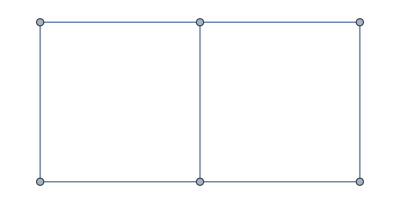

```mathematica
GridGraph[{2,3}]
```

```mathematica
EdgeConnectivity[GridGraph[{2,3}]]
```

2

```mathematica
FindEdgeCut[GridGraph[{2,3}]]
```

{4<->6,5<->6}

```mathematica
EdgeConnectivity[CompleteGraph[12]]
```

11

```mathematica
VertexConnectivity[CompleteGraph[12]]
```

11

```mathematica
FindVertexCut[]
```

```mathematica
Canvas[]
```

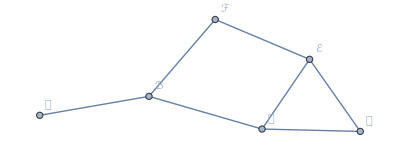

```mathematica
Graph[{𝒜<->ℬ,ℬ<->ℱ,ℬ<->𝒞,𝒞<->𝒟,𝒟<->ℰ,ℰ<->ℱ,ℰ<->𝒞},VertexLabels->Automatic]
```

```mathematica
FindVertexCut[Graph[{𝒜<->ℬ,ℬ<->ℱ,ℬ<->𝒞,𝒞<->𝒟,𝒟<->ℰ,ℰ<->ℱ,ℰ<->𝒞},VertexLabels->Automatic],ℱ,𝒟]
```

{ℬ,ℰ}